## 4 hysterons

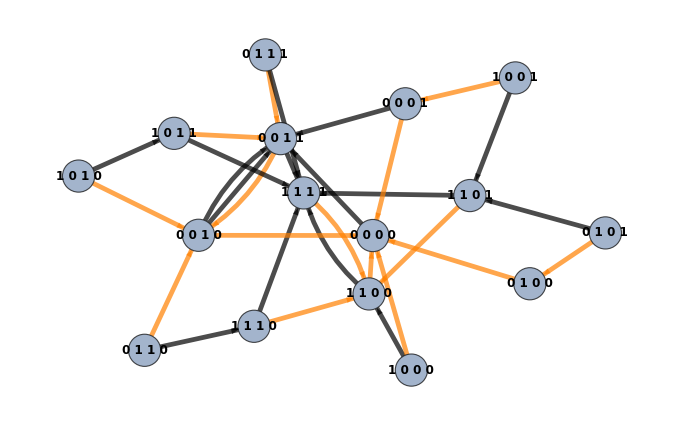

False

```mathematica
ClearAll@@Complement[Names["Global`*"],{"g2"}]


{a1,b1,c1,d1,a2,c2,a3,c3,a4,c4,k12,k13,k14,k23,k24,k34}={4,1,var,-1,4.1,-4,4.3,-3.9,3.9,-4.2,.5,0,0,-0.5,0,0.3};
var=-4.5;
equations={d1 g+c1 x1+b1 x1^2+a1 x1^3-k12 (-x1+x2)-k13 (-x1+x3)-k14 (-x1+x4),d2 g-k21 (x1-x2)+c2 x2+b2 x2^2+a2 x2^3-k23 (-x2+x3)-k24 (-x2+x4),d3 g-k31 (x1-x3)-k32 (x2-x3)+c3 x3+b3 x3^2+a3 x3^3-k34 (-x3+x4),d4 g-k41 (x1-x4)-k42 (x2-x4)-k43 (x3-x4)+c4 x4+b4 x4^2+a4 x4^3};
k21=k12;k31=k13;k41=k14;k32=k23;k42=k24;k43=k34;b2=b1;b3=b1;b4=b1;d2=d1;d3=d1;d4=d1;
jacobian=D[equations,{{x1,x2,x3,x4}}];

(*Set parameters here*)
bifurcationpts={x1,x2,x3,x4,g}/.NSolve[{equations==0,Det@jacobian==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3},{x1,x2,x3,x4,g},Reals];
poseigenvalpts={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Select[Table[Join[{bifurcationpts[[n,1]],bifurcationpts[[n,2]],bifurcationpts[[n,3]],bifurcationpts[[n,4]],bifurcationpts[[n,5]]},Eigenvalues[jacobian/.{x1->bifurcationpts[[n,1]],x2->bifurcationpts[[n,2]],x3->bifurcationpts[[n,3]],x4->bifurcationpts[[n,4]],g->bifurcationpts[[n,5]]}]],{n,1,Length@bifurcationpts}],#[[6]]>0&&#[[7]]>0&&#[[8]]>0&];
nullvectors=#[[7,4]]&/@Select[Table[Join[{bifurcationpts[[n,1]],bifurcationpts[[n,2]],bifurcationpts[[n,3]],bifurcationpts[[n,4]],bifurcationpts[[n,5]]},Eigensystem[jacobian/.{x1->bifurcationpts[[n,1]],x2->bifurcationpts[[n,2]],x3->bifurcationpts[[n,3]],x4->bifurcationpts[[n,4]],g->bifurcationpts[[n,5]]}]],{n,1,Length@bifurcationpts}],#[[6,1]]>0&&#[[6,2]]>0&&#[[6,3]]>0&];
maincondition=Table[(nullvectors[[n]].{D[D[equations[[1]],x1],x1]*nullvectors[[n,1]]^2,D[D[equations[[2]],x2],x2]*nullvectors[[n,2]]^2,D[D[equations[[3]],x3],x3]*nullvectors[[n,3]]^2,D[D[equations[[4]],x4],x4]*nullvectors[[n,4]]^2})/.{x1->poseigenvalpts[[n,1]],x2->poseigenvalpts[[n,2]],x3->poseigenvalpts[[n,3]],x4->poseigenvalpts[[n,4]]},{n,1,Length@nullvectors}];
states=Tally[{#[[1]],#[[2]],#[[3]],#[[4]]}&/@Map[If[#>=0,1,0]&,poseigenvalpts,{2}]];
creationpoints=Select[MapThread[Append,{poseigenvalpts,maincondition}],#[[6]]>0&];
annihilationpoints=Select[MapThread[Append,{poseigenvalpts,maincondition}],#[[6]]<0&];
timedequations=equations/.{x1->x1[t],x2->x2[t],x3->x3[t],x4->x4[t]};
{x1'[t],x2'[t],x3'[t],x4'[t]}==timedequations;

eps=0.005;
eps2=-0.005;
maxN=Length[annihilationpoints];
maxN2=Length[creationpoints];

results1=Table[Module[{gval,sol,x1f,x2f,x3f,x4f},gval=annihilationpoints[[n,5]]+eps;
sol=NDSolve[{x1'[t]==(-timedequations[[1]]/. g->gval),x2'[t]==(-timedequations[[2]]/. g->gval),x3'[t]==(-timedequations[[3]]/. g->gval),x4'[t]==(-timedequations[[4]]/. g->gval),x1[0]==annihilationpoints[[n,1]],x2[0]==annihilationpoints[[n,2]],x3[0]==annihilationpoints[[n,3]],x4[0]==annihilationpoints[[n,4]]},{x1,x2,x3,x4},{t,0,25}];
{x1[25]/. sol[[1]],x2[25]/. sol[[1]],x3[25]/. sol[[1]],x4[25]/. sol[[1]]}],{n,1,maxN}];
results2=Table[Module[{gval,sol,x1f,x2f,x3f,x4f},gval=creationpoints[[n,5]]+eps2;
sol=NDSolve[{x1'[t]==(-timedequations[[1]]/. g->gval),x2'[t]==(-timedequations[[2]]/. g->gval),x3'[t]==(-timedequations[[3]]/. g->gval),x4'[t]==(-timedequations[[4]]/. g->gval),x1[0]==creationpoints[[n,1]],x2[0]==creationpoints[[n,2]],x3[0]==creationpoints[[n,3]],x4[0]==creationpoints[[n,4]]},{x1,x2,x3,x4},{t,0,25}];
{x1[25]/. sol[[1]],x2[25]/. sol[[1]],x3[25]/. sol[[1]],x4[25]/. sol[[1]]}],{n,1,maxN2}];

list1a={#[[1]],#[[2]],#[[3]],#[[4]]}&/@Map[If[#>=0,1,0]&,annihilationpoints,{2}];
list2a=Map[If[#>=0,1,0]&,results1,{2}];
list1b={#[[1]],#[[2]],#[[3]],#[[4]]}&/@Map[If[#>=0,1,0]&,creationpoints,{2}];
list2b=Map[If[#>=0,1,0]&,results2,{2}];
(*Convert 4-tuples to space-separated strings*)
toStr=StringJoin@Riffle[ToString/@#," "]&;
list1aStr=toStr/@list1a;
list2aStr=toStr/@list2a;
list1bStr=toStr/@list1b;
list2bStr=toStr/@list2b;
(*Arrowhead size*)
xx=0.04;
edges1=MapThread[Style[#1->#2,Black,Arrowheads[xx],Thickness[0.005]]&,{list1aStr,list2aStr}];
edges2=MapThread[Style[#1->#2,Orange,Arrowheads[xx],Thickness[0.005]]&,{list1bStr,list2bStr}];
(*Combine and draw the graph*)
g1=Graph[Join[edges1,edges2],VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Bold,12],VertexSize->0.55]

IsomorphicGraphQ[g1,g2]
```

```mathematica
Complement[EdgeList[g1],EdgeList[g2]]       (*Edges in g1 not g2*)
Complement[EdgeList[g2],EdgeList[g1]]       (*Edges in g2 not g1*)
Complement[VertexList[g1],VertexList[g2]]   (*In g1 but not g2*)
Complement[VertexList[g2],VertexList[g1]]   (*In g2 but not g1*)
```

{0 1 1 1->1 1 1 1}

{}

{}

{}

```mathematica
g2=g1;
```

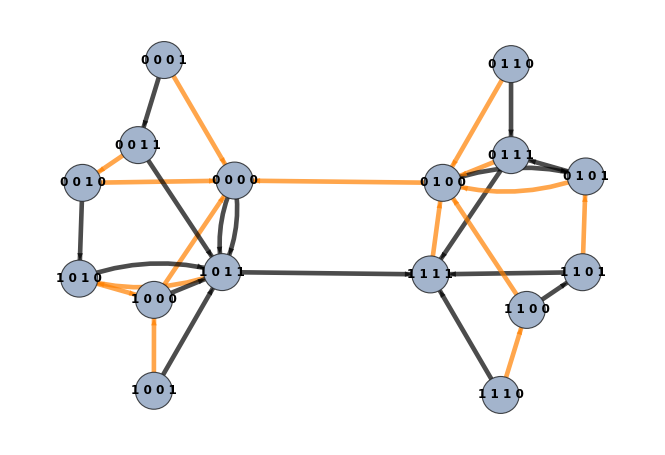

```mathematica
g2
```

## 2 hysterons

```mathematica
{-4.29936358873011,-4.299363588730108,-4.156977167021913,-4.156977167021911,-3.932147759286357,-3.9226281234561027,-3.879262544645338,-3.873868096093057,-3.8738680960930556,-3.597141497481379,-3.5516673269878827}
```

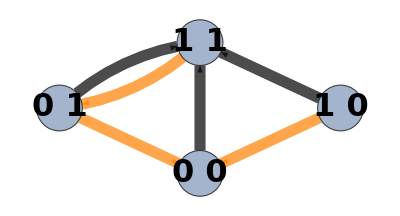

```mathematica
{a1,b1,c1,d1,a2,c2,k12}={4,1.2,var,-1,4.3,-4,0.2};var=-3.6;
equations={d1 g+2c1 x1+b1 x1^2+a1 x1^3-k12 (-x1+x2),d2 g-k21 (x1-x2)+2c2 x2+b2 x2^2+a2 x2^3};
k21=k12;k31=k13;k41=k14;k32=k23;k42=k24;k43=k34;b2=1;b3=b1;b4=b1;d2=d1;d3=d1;d4=d1;
jacobian=D[equations,{{x1,x2}}];bifurcationpts={x1,x2,g}/.NSolve[{equations==0,Det@jacobian==0&&Abs[x1]<3&&Abs[x2]<3},{x1,x2,g},Reals];
poseigenvalpts={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Select[Table[Join[{bifurcationpts[[n,1]],bifurcationpts[[n,2]],bifurcationpts[[n,3]]},Eigenvalues[jacobian/.{x1->bifurcationpts[[n,1]],x2->bifurcationpts[[n,2]],g->bifurcationpts[[n,3]]}]],{n,1,Length@bifurcationpts}],#[[4]]>0&];
nullvectors=#[[5,2]]&/@Select[Table[Join[{bifurcationpts[[n,1]],bifurcationpts[[n,2]],bifurcationpts[[n,3]]},Eigensystem[jacobian/.{x1->bifurcationpts[[n,1]],x2->bifurcationpts[[n,2]],g->bifurcationpts[[n,3]]}]],{n,1,Length@bifurcationpts}],#[[4,1]]>0&];
maincondition=Table[(nullvectors[[n]].{D[D[equations[[1]],x1],x1]*nullvectors[[n,1]]^2,D[D[equations[[2]],x2],x2]*nullvectors[[n,2]]^2})/.{x1->poseigenvalpts[[n,1]],x2->poseigenvalpts[[n,2]]},{n,1,Length@nullvectors}];
states=Tally[{#[[1]],#[[2]]}&/@Map[If[#>=0,1,0]&,poseigenvalpts,{2}]];
creationpoints=Select[MapThread[Append,{poseigenvalpts,maincondition}],#[[6]]<0&];
annihilationpoints=Select[MapThread[Append,{poseigenvalpts,maincondition}],#[[6]]>0&];
timedequations=equations/.{x1->x1[t],x2->x2[t]};
{x1'[t],x2'[t]}==timedequations;
eps=0.00068;
eps2=-0.00068;
maxN=Length[annihilationpoints];
maxN2=Length[creationpoints];
results1=Table[Module[{gval,sol,x1f,x2f},gval=annihilationpoints[[n,3]]+eps;
sol=NDSolve[{x1'[t]==(-timedequations[[1]]/. g->gval),x2'[t]==(-timedequations[[2]]/. g->gval),x1[0]==annihilationpoints[[n,1]],x2[0]==annihilationpoints[[n,2]]},{x1,x2},{t,0,25}];
{x1[25]/. sol[[1]],x2[25]/. sol[[1]]}],{n,1,maxN}];
results2=Table[Module[{gval,sol,x1f,x2f},gval=creationpoints[[n,3]]+eps2;
sol=NDSolve[{x1'[t]==(-timedequations[[1]]/. g->gval),x2'[t]==(-timedequations[[2]]/. g->gval),x1[0]==creationpoints[[n,1]],x2[0]==creationpoints[[n,2]]},{x1,x2},{t,0,25}];
{x1[25]/. sol[[1]],x2[25]/. sol[[1]]}],{n,1,maxN2}];
list1a={#[[1]],#[[2]]}&/@Map[If[#>=0,1,0]&,annihilationpoints,{2}];list2a=Map[If[#>=0,1,0]&,results1,{2}];
list1b={#[[1]],#[[2]]}&/@Map[If[#>=0,1,0]&,creationpoints,{2}];list2b=Map[If[#>=0,1,0]&,results2,{2}];
toStr=StringJoin@Riffle[ToString/@#," "]&;
list1aStr=toStr/@list1a;list2aStr=toStr/@list2a;list1bStr=toStr/@list1b;list2bStr=toStr/@list2b;xx=0.14;
edges1=MapThread[Style[#1->#2,Black,Arrowheads[xx],Thickness[0.02]]&,{list1aStr,list2aStr}];
edges2=MapThread[Style[#1->#2,Orange,Arrowheads[xx],Thickness[0.02]]&,{list1bStr,list2bStr}];
(*Combine and draw the graph*)
g1=Graph[Join[edges1,edges2],VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Bold,32],VertexSize->0.35]
```

## Cusp points

```mathematica
Clear[var];{a1,b1,c1,d1,a2,c2,k12}={4,1.2,var,-1,4.3,-4,0.45};
equations={d1 g+2c1 x1+b1 x1^2+a1 x1^3-k12 (-x1+x2),d2 g-k21 (x1-x2)+2c2 x2+b2 x2^2+a2 x2^3};
k21=k12;k31=k13;k41=k14;k32=k23;k42=k24;k43=k34;b2=1;b3=b1;b4=b1;d2=d1;d3=d1;d4=d1;
jacobian=D[equations,{{x1,x2}}];
nullvector=(NullSpace[{{A11,A12},{A12,A12^2/A11}}])/.{A11->D[equations[[1]],x1],A12->D[equations[[1]],x2]};
cusppoints={x1,x2,g,var}/.NSolve[{equations==0&&Det@jacobian==0&&nullvector.{D[D[equations[[1]],x1],x1]*nullvector[[1,1]]^2,D[D[equations[[2]],x2],x2]*nullvector[[1,2]]^2}==0&&Abs[x1]<3&&Abs[x2]<3&&var<-1},{x1,x2,g,var},Reals];
eigenvalofcusp=#[[1]]&/@Table[Eigenvalues[jacobian/.{x1->cusppoints[[n,1]],x2->cusppoints[[n,2]],g->cusppoints[[n,3]],var->cusppoints[[n,4]]}],{n,1,Length@cusppoints}];
selectedcusps={#[[3]],#[[4]]}&/@Select[MapThread[Append,{cusppoints,eigenvalofcusp}],#[[5]]>0&];
crossingpoints={x1,x2,x11,x22,g,var}/.NSolve[{equations==0&&Det@jacobian==0&&(equations/.{x1->x11,x2->x22})==0&&(Det[jacobian/.{x1->x11,x2->x22}])==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x11]<3&&Abs[x22]<3&&var<-3.4},{x1,x2,x11,x22,g,var},Reals];
eigenvalofcrossing=({#[[1,1]],#[[2,1]]}&)/@Table[{Eigenvalues[jacobian/.{x1->crossingpoints[[n,1]],x2->crossingpoints[[n,2]],g->crossingpoints[[n,5]],var->crossingpoints[[n,6]]}],Eigenvalues[jacobian/.{x1->crossingpoints[[n,3]],x2->crossingpoints[[n,4]],g->crossingpoints[[n,5]],var->crossingpoints[[n,6]]}]},{n,1,Length@crossingpoints}];
selectedcrossings={#[[5]],#[[6]]}&/@Select[MapThread[Append,{crossingpoints,eigenvalofcrossing}],#[[7,1]]>0&&#[[7,2]]>0&];
ptstocheck=DeleteDuplicates[Chop@Sort@Join[selectedcrossings,selectedcusps]];
DeleteDuplicates[Chop[SortBy[Join[selectedcusps,selectedcrossings],#[[2]]&]]]
```

{{-3.76722,-4.79485},{5.02141,-4.45207},{-2.80148,-4.13526},{-2.80148,-4.13526},{4.08132,-3.93061},{4.08132,-3.93061}}

```mathematica
Clear[var];{a1,b1,c1,d1,a2,c2,k12}={4,1.2,var,-1,4.3,-4,var2};
equations={d1 g+2c1 x1+b1 x1^2+a1 x1^3-k12 (-x1+x2),d2 g-k21 (x1-x2)+2c2 x2+b2 x2^2+a2 x2^3};
k21=k12;k31=k13;k41=k14;k32=k23;k42=k24;k43=k34;b2=1;b3=b1;b4=b1;d2=d1;d3=d1;d4=d1;
jacobian=D[equations,{{x1,x2}}];
nullvector=(NullSpace[{{A11,A12},{A12,A12^2/A11}}])/.{A11->D[equations[[1]],x1],A12->D[equations[[1]],x2]};
(*cusppoints={x1,x2,g,var}/.NSolve[{equations==0&&Det@jacobian==0&&nullvector.{D[D[equations[[1]],x1],x1]*nullvector[[1,1]]^2,D[D[equations[[2]],x2],x2]*nullvector[[1,2]]^2}==0&&Abs[x1]<3&&Abs[x2]<3&&var<-1},{x1,x2,g,var},Reals];
crossingpoints={x1,x2,x11,x22,g,var}/.NSolve[{equations==0&&Det@jacobian==0&&(equations/.{x1->x11,x2->x22})==0&&(Det[jacobian/.{x1->x11,x2->x22}])==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x11]<3&&Abs[x22]<3&&var<-3.4},{x1,x2,x11,x22,g,var},Reals];*)
```

```mathematica
triplecrossing={x1,x2,x3,x4,x5,x6,g,var,var2}/.NSolve[{equations==0&&Det@jacobian==0&&(equations/.{x1->x3,x2->x4})==0&&(Det[jacobian/.{x1->x3,x2->x4}])==0&&(equations/.{x1->x5,x2->x6})==0&&(Det[jacobian/.{x1->x5,x2->x6}])==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3&&Abs[x5]<3&&Abs[x6]<3&&-4.5<=var<=-3.5&&-.5<=var2<=.5},{x1,x2,x3,x4,x5,x6,g,var,var2},Reals]
```

{{-3.79407,0},{-3.79407,0},{-3.79407,0},{-3.79407,0},{-3.79407,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0}}

```mathematica
DeleteDuplicates[triplecrossing]
```

{{-3.79407,0},{-3.79407,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0}}

```mathematica
twocrossings={x1,x2,x3,x4,x5,x6,x7,x8,g,g2,var,var2}/.NSolve[{equations==0&&Det@jacobian==0&&(equations/.{x1->x3,x2->x4})==0&&(Det[jacobian/.{x1->x3,x2->x4}])==0&&(equations/.{x1->x5,x2->x6,g->g2})==0&&(Det[jacobian/.{x1->x5,x2->x6,g->g2}])==0&&(equations/.{x1->x7,x2->x8,g->g2})==0&&(Det[jacobian/.{x1->x7,x2->x8,g->g2}])==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3&&Abs[x5]<3&&Abs[x6]<3&&Abs[x7]<3&&Abs[x8]<3&&-4.5<=var<=-3.5&&-.5<=var2<=.5},{x1,x2,x3,x4,x5,x6,x7,x8,g,g2,var,var2},Reals];
```

```mathematica
updtwocrossing=DeleteDuplicates[twocrossings]
```

{{-3.99607,0.139658},{-3.99607,0.139658},{-3.99607,0.139658},{-3.99607,0.139658},{-3.98751,0.133903},{-3.98751,0.133903},{-3.98751,0.133903},{-3.98751,0.133903},{-3.98751,0.133903},{-3.88816,0.0662833},{-3.88816,0.0662833},{-3.88816,0.0662833},{-3.88816,0.0662833},{-3.88816,0.0662833},{-3.88816,0.0662833},{-3.88296,0.0626992},{-3.88296,0.0626992},{-3.88296,0.0626992},{-3.88296,0.0626992},{-3.88296,0.0626992},{-3.88296,0.0626992},{-3.79407,0},{-3.99449,0},{-3.79407,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.79407,0},{-3.99449,0},{-3.79407,0},{-3.99449,0},{-3.99449,0},{-3.79407,0},{-3.79407,0},{-3.79407,0},{-3.99449,0},{-3.99449,0},{-3.79407,0},{-3.79407,0},{-3.79407,0},{-3.87784,0.0655157},{-3.87784,0.0655157},{-3.87784,0.0655157},{-3.87784,0.0655157},{-3.87784,0.0655157},{-3.87784,0.0655157},{-3.88294,0.0696405},{-3.88294,0.0696405},{-3.88294,0.0696405},{-3.88294,0.0696405},{-3.88294,0.0696405},{-3.88294,0.0696405},{-3.88294,0.0696405},{-3.88294,0.0696405},{-3.98639,0.155669},{-3.98639,0.155669},{-3.98639,0.155669},{-3.98639,0.155669},{-3.98639,0.155669},{-3.98639,0.155669},{-3.98639,0.155669},{-3.98639,0.155669},{-3.99634,0.164179},{-3.99634,0.164179},{-3.99634,0.164179},{-3.99634,0.164179},{-3.99634,0.164179},{-3.79623,0.109871},{-3.79623,0.109871},{-3.79623,0.109871},{-3.79623,0.109871},{-3.79623,0.109871},{-3.79657,0.126394},{-3.79657,0.126394},{-3.79657,0.126394},{-3.79657,0.126394},{-3.79657,0.126394},{-3.79657,0.126394},{-3.79657,0.126394},{-3.79657,0.126394},{-3.99449,5.25329×10^-7},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,2.08112×10^-10},{-3.99449,2.6824×10^-10},{-3.99449,2.72293×10^-10},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,0},{-3.99449,1.63105×10^-10}}

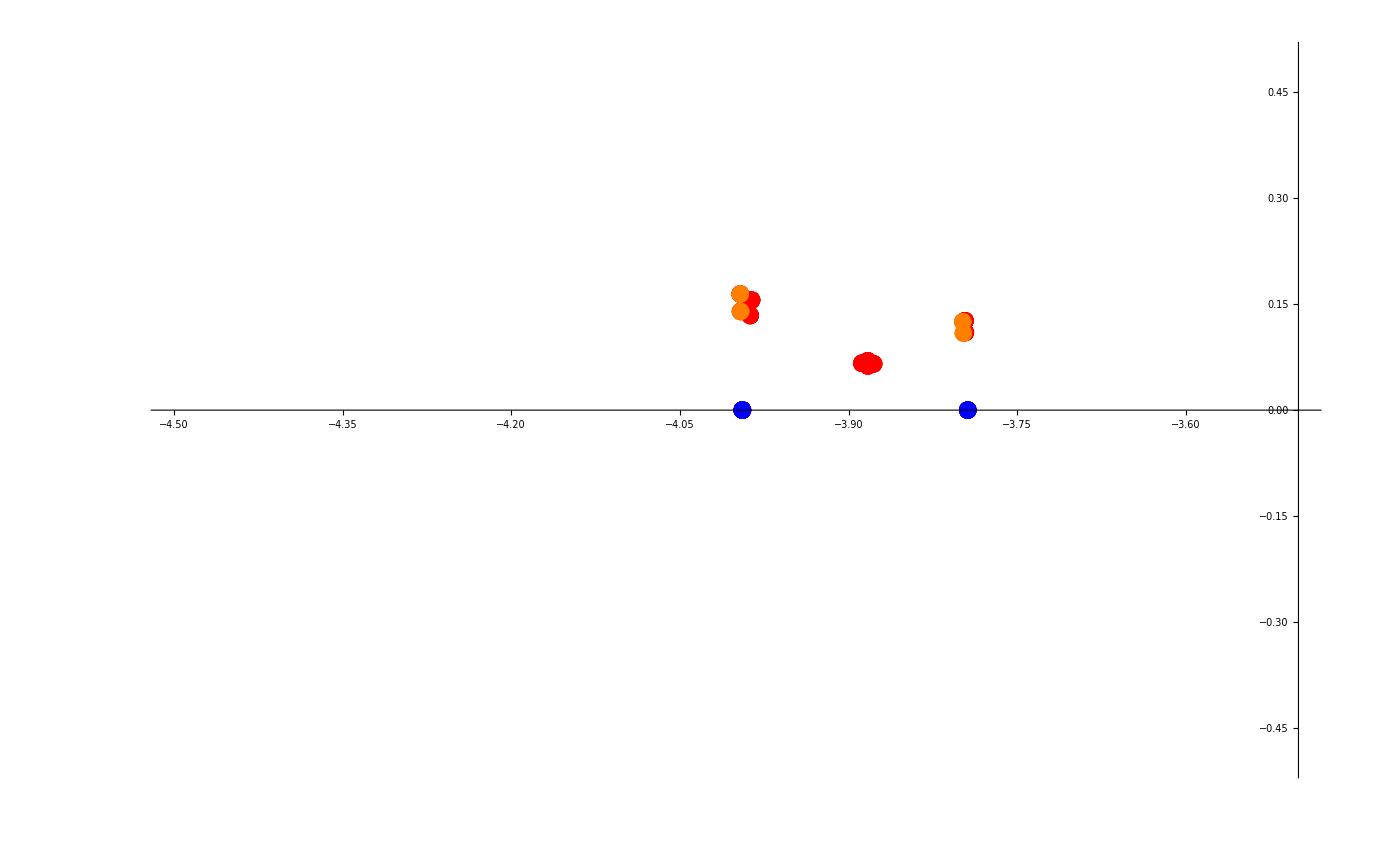

```mathematica
ListPlot[{updtwocrossing,triplecrossing,doublecusppoints},PlotStyle->{Red,Blue,Orange},PlotRange->{{-4.5,-3.5},{-.5,.5}}]
```

```mathematica
doublecusppoints={x1,x2,x3,x4,x5,x6,g,g2,var,var2}/.NSolve[{equations==0&&Det@jacobian==0&&nullvector.{D[D[equations[[1]],x1],x1]*nullvector[[1,1]]^2,D[D[equations[[2]],x2],x2]*nullvector[[1,2]]^2}==0&&(equations/.{x1->x3,x2->x4,g->g2})==0&&(Det[jacobian/.{x1->x3,x2->x4,g->g2}])==0&&(equations/.{x1->x5,x2->x6,g->g2})==0&&(Det[jacobian/.{x1->x5,x2->x6,g->g2}])==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3&&-4.5<=var<=-3.5&&-.5<=var2<=.5},{x1,x2,x3,x4,x5,x6,g,g2,var,var2},Reals]
```

{{-0.890589,-0.857975,-1.69313,0.708459,0.696376,0.863617,4.88771,-3.37519,-3.79802,0.108906},{-0.890589,-0.857975,0.696376,0.863617,-1.69313,0.708459,4.88771,-3.37519,-3.79802,0.108906},{-0.888967,-0.856356,-1.68985,0.707672,0.695158,0.529162,4.88785,-3.3369,-3.79861,0.125025},{-0.888967,-0.856356,0.695158,0.529162,-1.68985,0.707672,4.88785,-3.3369,-3.79861,0.125025},{0.708001,0.699906,-1.09215,-0.862205,-0.915133,1.49239,-3.6362,4.91702,-3.99607,0.139658},{0.708001,0.699906,-0.915133,1.49239,-1.09215,-0.862205,-3.6362,4.91702,-3.99607,0.139658},{0.70551,0.697443,-0.706167,-0.860365,-0.913923,1.48749,-3.63565,4.85931,-3.99634,0.164179},{0.70551,0.697443,-0.913923,1.48749,-0.706167,-0.860365,-3.63565,4.85931,-3.99634,0.164179}}

```mathematica
eigs5=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[1]],x2->#[[2]],g->#[[7]],var->#[[9]],var2->#[[10]]}&/@doublecusppoints)[[n]]],{n,1,Length@doublecusppoints}]
eigs6=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[3]],x2->#[[4]],g->#[[8]],var->#[[9]],var2->#[[10]]}&/@doublecusppoints)[[n]]],{n,1,Length@doublecusppoints}]
eigs7=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[5]],x2->#[[6]],g->#[[8]],var->#[[9]],var2->#[[10]]}&/@doublecusppoints)[[n]]],{n,1,Length@doublecusppoints}]
```

{-0.217855,-0.217855,-0.2501,-0.2501,-0.279333,-0.279333,-0.328378,-0.328378}

{22.8502,3.46084,22.7398,-3.20937,3.84493,23.8564,-3.54687,23.683}

{3.46084,22.8502,-3.20937,22.7398,23.8564,3.84493,23.683,-3.54687}

```mathematica
eigs1=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[1]],x2->#[[2]],g->#[[9]],var->#[[11]],var2->#[[12]]}&/@updtwocrossing)[[n]]],{n,1,Length@updtwocrossing}];
eigs2=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[3]],x2->#[[4]],g->#[[9]],var->#[[11]],var2->#[[12]]}&/@updtwocrossing)[[n]]],{n,1,Length@updtwocrossing}];
eigs3=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[5]],x2->#[[6]],g->#[[10]],var->#[[11]],var2->#[[12]]}&/@updtwocrossing)[[n]]],{n,1,Length@updtwocrossing}];
eigs4=#[[1]]&/@Table[Eigenvalues[(jacobian/.{x1->#[[7]],x2->#[[8]],g->#[[10]],var->#[[11]],var2->#[[12]]}&/@updtwocrossing)[[n]]],{n,1,Length@updtwocrossing}];
eigs1234=Thread[{eigs1,eigs2,eigs3,eigs4}];
```

```mathematica
Select[eigs1234,#[[1]]>0&&#[[2]]>0&&#[[3]]>0&&#[[4]]>0&]
```

{{23.2746,23.3676,3.75937,23.8711},{3.75937,23.8711,23.2746,23.3676},{23.2746,23.3676,23.8711,3.75937},{23.3676,23.2746,3.75937,23.8711},{23.8711,3.75937,23.2746,23.3676},{23.4822,2.61015,24.0574,2.51621},{23.4822,2.61015,2.51621,24.0574},{2.61015,23.4822,24.0574,2.51621},{2.61015,23.4822,2.51621,24.0574},{24.0574,2.51621,2.61015,23.4822},{24.0574,2.51621,23.4822,2.61015},{24.2326,24.3269,4.07561,23.7295},{24.3269,24.2326,4.07561,23.7295},{4.07561,23.7295,24.3269,24.2326},{3.64002,23.7488,24.2326,23.1244},{23.7295,4.07561,24.2326,24.3269},{23.7488,3.64002,24.2326,23.1244},{24.2326,24.3269,23.7295,4.07561},{23.7488,3.64002,23.1244,24.2326},{3.64002,23.7488,23.1244,24.2326},{24.2326,1.46216×10^-6,23.7295,4.07561},{24.2326,23.1244,23.1244,1.78534×10^-6},{24.3269,24.2326,23.7295,4.07561},{23.1244,24.2326,24.2326,1.2624×10^-6},{24.2326,23.1244,1.17885×10^-6,24.2326},{23.1244,24.2326,7.58046×10^-7,23.1244},{23.1244,24.2326,24.2326,1.26586×10^-6},{4.07561,23.7295,24.2326,24.3269},{23.1244,24.2326,3.64002,23.7488},{4.07561,23.7295,9.67986×10^-7,24.2326},{4.07561,23.7295,24.2326,1.31448×10^-6},{4.07561,23.7295,24.2326,1.3125×10^-6},{4.07561,23.7295,1.09418×10^-6,1.04645×10^-6},{23.1244,1.10446×10^-6,23.7488,3.64002},{4.07561,23.7295,1.26626×10^-6,24.3269},{24.2326,23.1244,3.64002,23.7488},{23.7295,4.07561,6.75951×10^-7,6.59847×10^-7},{23.1244,24.2326,3.64002,23.7488},{23.1244,24.2326,23.7488,3.64002},{23.4579,22.3738,22.837,3.47642},{22.3738,23.4579,22.837,3.47642},{3.47642,22.837,23.4579,22.3738},{22.837,3.47642,22.3738,23.4579},{22.3738,23.4579,3.47642,22.837},{1.51802×10^-6,24.3269,24.3269,24.2326},{5.33048×10^-7,24.3269,24.2326,8.14454×10^-7},{1.02014×10^-6,24.3269,24.2326,24.3269},{24.3269,1.11026×10^-6,24.2326,1.05369×10^-6},{24.2326,24.3269,1.85224×10^-6,24.3269},{24.2326,1.65175×10^-6,1.56749×10^-6,24.3269},{24.2326,1.6567×10^-6,1.57496×10^-6,24.3269},{24.2326,1.55556×10^-6,24.3269,1.73624×10^-6},{24.3269,24.2326,1.10802×10^-6,1.0563×10^-6},{1.1251×10^-6,24.2326,24.3269,9.1516×10^-7},{1.16413×10^-6,24.2326,24.3269,24.2326},{24.2326,1.52941×10^-6,24.3269,1.69659×10^-6},{1.02385×10^-6,24.2326,24.2326,24.3269},{24.2326,1.50977×10^-6,1.4273×10^-6,24.3269},{1.14736×10^-6,24.2326,24.3269,9.33113×10^-7},{24.3269,24.2326,24.2326,6.96819×10^-7},{24.3269,24.2326,24.3269,7.0844×10^-7},{24.3269,6.68486×10^-7,6.88202×10^-7,6.46798×10^-7},{24.2326,24.3269,24.2326,9.47799×10^-7},{24.2326,24.3269,6.45243×10^-7,6.05375×10^-7},{24.2326,6.6401×10^-7,6.60781×10^-7,6.42849×10^-7},{24.2326,6.57297×10^-7,6.85417×10^-7,6.49561×10^-7}}

```mathematica
eigs1
```

{-0.279334,-0.279334,3.84493,23.8564,23.2746,3.75937,23.2746,23.3676,23.8711,2.59068,23.4761,23.4761,-2.41458,-2.41458,24.0478,24.0478,23.4822,23.4822,2.61015,2.61015,24.0574,24.0574,24.2326,24.2326,24.2326,24.3269,4.07561,24.2326,3.64002,24.2326,23.1244,23.1244,24.2326,23.7295,24.3269,23.7488,23.7488,24.2326,-3.15625,4.07561,24.2326,24.2326,23.7488,23.1244,3.64002,24.3269,3.64002,-3.15625,-6.75071×10^-7,24.2326,24.2326,24.2326,24.2326,24.2326,24.3269,24.2326,24.3269,3.64002,-7.15728×10^-7,23.7295,-3.15625,3.64002,24.2326,3.64002,23.1244,1.08333×10^-6,-3.15625,3.64002,23.1244,24.2326,24.2326,3.64002,3.64002,23.1244,23.1244,-3.15625,23.1244,3.64002,4.07561,-3.47822,24.2326,23.1244,23.7295,-3.47822,-3.47822,-3.47822,-3.47822,23.7295,-3.47822,-3.47822,-3.47822,-3.47822,23.1244,4.07561,23.1244,23.7295,24.2326,4.07561,4.07561,4.07561,4.07561,4.07561,4.07561,4.07561,4.07561,4.07561,23.1244,-3.15625,24.2326,4.07561,-3.47822,23.7295,-3.47822,-3.47822,-3.47822,4.07561,24.2326,24.2326,23.7295,23.7295,23.7295,23.7295,23.1244,24.2326,23.1244,-5.63606×10^-7,23.1244,3.64002,3.64002,-3.15625,-3.15625,-2.31644,23.4439,23.4439,2.66953,2.66953,24.0218,-2.31644,-2.3841,-2.3841,-2.3841,23.4337,24.008,-2.46987,24.008,24.008,23.2117,23.1189,23.1189,23.2117,23.1189,-3.46208,23.713,23.713,-3.46208,-0.328378,-0.328378,-3.54687,23.683,-3.54687,23.4579,22.3738,3.47642,22.837,22.3738,-3.22463,22.7228,22.7228,23.3414,22.261,22.261,23.3414,22.261,-1.15214×10^-6,24.2326,-0.0000620927,-0.0000451476,24.2326,2.4093×10^-6,-6.23649×10^-7,6.91882×10^-7,24.3269,24.2326,1.51802×10^-6,7.85723×10^-7,5.33048×10^-7,24.2326,1.02014×10^-6,-1.41445×10^-6,-5.74467×10^-7,24.3269,-8.1462×10^-7,24.2326,-2.2259×10^-6,-1.23996×10^-6,-7.89214×10^-7,24.3269,24.2326,24.2326,24.3269,5.31309×10^-7,24.2326,-4.87002×10^-7,24.2326,24.2326,24.2326,24.2326,-1.1879×10^-6,24.3269,24.2326,-1.14943×10^-6,-8.24738×10^-7,24.2326,24.2326,24.2326,24.3269,24.3269,1.1251×10^-6,24.3269,1.16413×10^-6,-1.14736×10^-6,24.2326,-7.73597×10^-7,1.30128×10^-6,1.02385×10^-6,8.24312×10^-7,24.3269,-1.3439×10^-6,24.2326,-2.0854×10^-6,1.84405×10^-6,24.2326,24.2326,24.2326,1.14736×10^-6,24.3269,24.3269,24.3269,24.3269,24.2326,24.3269,1.1319×10^-6,8.50415×10^-7,-1.79709×10^-6,24.3269,24.3269,1.32845×10^-6,-9.33397×10^-7,24.2326,24.3269,24.2326,1.3145×10^-6,24.3269,1.34343×10^-6,24.2326,24.2326,-8.96605×10^-7,0.0000269398,0.0000279915,0.0000317836,24.3269,24.2326,24.3269,0.0000907358,0.0000940014,0.000095596,24.3269,0.000128177}